## functions

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinuteString[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
MinuteOfDayToHourAndMinuteList[minuteOfDay_]:={IntegerPart[minuteOfDay/60],FractionalPart[minuteOfDay/60]60}
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
DateExtend[dateObject_,hour_,minute_]:=DateObject[Flatten[{DateList[dateObject][[1;;3]],{hour,minute}}]]
```

```mathematica
(*Function to normalize DateObjects to the same granularity*)
NormalizeDate[date_]:=DateObject[DateList[date][[1;;3]]]

(*Function to find the index of the first element not less than a given date*)
FindFirstIndexNotLessThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<normDate,low=mid+1,high=mid];];
low]

(*Function to find the index of the first element greater than a given date*)
FindFirstIndexGreaterThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<=normDate,low=mid+1,high=mid];];
low]

(*Define the function to select elements by date range*)
SelectElementsByDateRange[list_,startDate_,endDate_]:=Module[{startIndex,endIndex,normStartDate,normEndDate},(*Normalize dates*)normStartDate=NormalizeDate[startDate];
normEndDate=NormalizeDate[endDate];
(*Find the starting and ending indices*)startIndex=FindFirstIndexNotLessThan[list,normStartDate];
endIndex=FindFirstIndexGreaterThan[list,normEndDate];
(*Return the sublist within the range*)list[[startIndex;;endIndex-1]]]
```

## misc

## heatmeter read-in

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinute[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
path=formattedDataRoot;
fileName="heat_stock_net.csv";
lastLoadDay=Module[
{dirs,sortedDirs,foundFile},
(*Get list of directories*)
dirs=FileNames["*",path];
(*Sort directories in decreasing order*)
sortedDirs=Sort[dirs,DateObject[#1]>DateObject[#2]&];
(*Search for the file*)
foundFile=SelectFirst[sortedDirs,FileExistsQ[FileNameJoin[{#,fileName}]]&];
StringSplit[foundFile,"\\"][[-1]]
];
loadDayStamps=Map[StringRiffle[Map[ToStringWithDateCorrection,#[[1;;3]]],"-"]&,DateRange[{2024,2,1},DateObject[lastLoadDay]]];
heatStockDataOriginal=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
heatStockDataNet=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
badDays=Flatten[Intersection[Flatten[Position[heatStockDataOriginal,$Failed]],Flatten[Position[heatStockDataNet,$Failed]]]];
goodDays=Complement[Range[Length[loadDayStamps]],badDays];
Manipulate[
Module[
{dayN,timeStamps},
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=Map[
HourAndMinuteToMinuteOfDay[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
];
Grid[{
{"day","original","net","diff"},
{
loadDayStamps[[dayN]],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={}&&Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]]-heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"]
},
Table[ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Nothing]
},
Joined->True,PlotRange->All,Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.25]}&,Range[0,24 60, 120]],Automatic},ImageSize->250,PlotLabel->"cycle "<>ToString[cycle],Prolog->{If[showCaptures,{Pink,Thin,Map[Line[{{#,0},{#,10000}}]&,timeStamps]}]}
],{cycle,1,4}]
}]
],
{showCaptures,{False,True}},
{{day,loadDayStamps[[goodDays]][[-1]]},loadDayStamps[[goodDays]]}
]
```

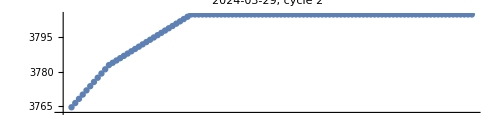
-Graphics-
1500 | 1510 | 1520 | 1530 | 1540 | 1550 | 1600 | 1610 | 1620 | 1630 | 1640 | 1650 | 1700 | 1710 | 1720 | 1730 | 1740 | 1750 | 1800 | 1810 | 1820 | 1830 | 1840 | 1850 | 1900 | 1910 | 1920 | 1930 | 1940 | 1950 | 2000 | 2010 | 2020 | 2030 | 2040 | 2050 | 2100 | 2110 | 2120 | 2130 | 2140 | 2150 | 2200 | 2210 | 2220 | 2230 | 2240 | 2250 | 2300 | 2310 | 2320 | 2330 | 2340 | 2350
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
cycle=2;timeSpan={15,24}100;
day=loadDayStamps[[goodDays]][[-1]];
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=DeleteDuplicates[Map[
ToExpression[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
]];
cycleImagesForTimeSpan=Map[
Import[rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"<>ToStringWithDateCorrection[#,4]<>"_"<>ToString[cycle]<>".png"]
&,Select[timeStamps,Between[#,timeSpan]&]];
{
ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing]
},
Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.5]}&,Range[0,24 60, 10]],Automatic},ImageSize->500,AspectRatio->0.25,PlotLabel->day<>", cycle "<>ToString[cycle]
],
{Select[timeStamps,Between[#,timeSpan]&],cycleImagesForTimeSpan}//Grid
}//Column
```

```mathematica
heatFlowDataOriginal=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow.csv"]&,
loadDayStamps];
```

```mathematica
heatFlowDataNet=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow_net.csv"]&,
loadDayStamps];
```

```mathematica
Table[
Table[
ListPlot[
{
Transpose[Transpose[heatFlowDataOriginal[[day]]][[{1,1+cycle}]]],
Transpose[Transpose[heatFlowDataNet[[day]]][[{1,1+cycle}]]]
},
Joined->True,PlotRange->All
]
,{cycle,1,4}]
,{day,goodDays}]//Grid
```

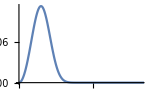
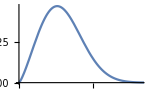
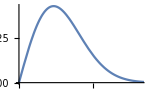
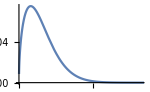

```mathematica
weibullParameters={
{3,10.3,0.001},
{2.3,20,0.001},
{2,20,0.001},
{1.5,10,0.001}
};
Table[Plot[
PDF[WeibullDistribution[weibullParameters[[cycle]][[1]],weibullParameters[[cycle]][[2]],weibullParameters[[cycle]][[3]]],power],{power,0,100},PlotRange->{{0,50},All},ImageSize->150
],{cycle,1,4}]//Row
```

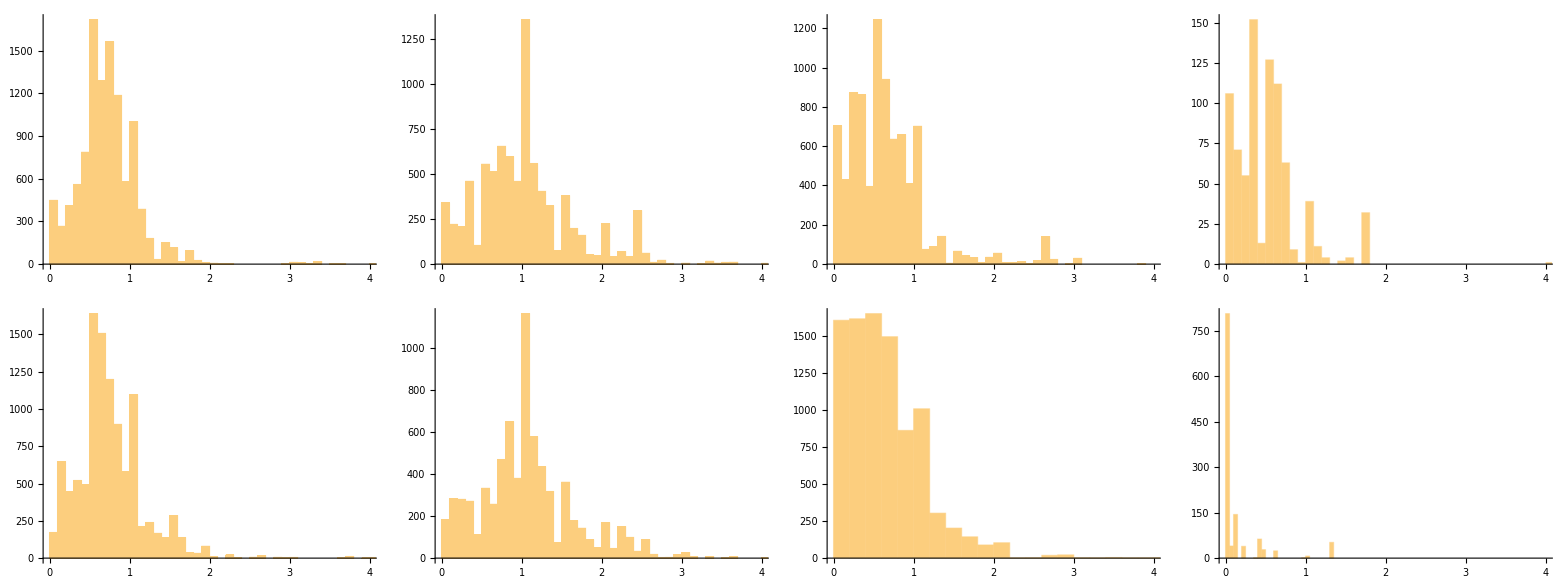

```mathematica
{
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataOriginal[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}],
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataNet[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}]
}//Grid
```

## adatok

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

## hő

```mathematica
heatDataDays=Map[DateObject,DateRange[{2023,11,22},{2024,3,29}]];
```

```mathematica
heatStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatDataDays]]];
```

```mathematica
heatStockDated=Map[Flatten[#,1]&,Transpose[Table[
Module[
{dayDateList},
dayDateList=DateList[heatDataDays[[dayN]]];
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatStockLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],heatStockLine[[2;;5]]}]
,{heatStockLine,heatStockPre[[dayN]]}]]
]
,{dayN,1,Length[heatDataDays]}]]];
(*1-es kör átfordulás: jan 20-21*)
(*2-es kör átfordulás: feb 4-5*)
```

```mathematica
cycle=2;
Map[
SortBy[heatStock[[cycle]][[#[[1]];;#[[1]]+1]],First]&,
Map[Position[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#][[1]]&,Select[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#<-10&]]
]
```

{{{Thu 14 Dec 2023 23:55:00GMT+2,4247},{Fri 15 Dec 2023 00:00:00GMT+2,4228.81}},{{Sun 4 Feb 2024 23:55:00GMT+2,9937},{Mon 5 Feb 2024 00:00:00GMT+2,125.}}}

```mathematica
heatStockDated[[1]]=Map[
If[
DateObject[{2024,1,20,23,59}]<#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[1]]];
```

```mathematica
heatStockDated[[2]]=Quiet[Map[
If[
DateObject[{2024,2,4,23,59}]<=#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[2]]]];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDated.mx",heatStock];
```

```mathematica
heatStockSeason=Table[
Transpose[{
Transpose[heatStockDated[[cycle]]][[1]],
Transpose[heatStockDated[[cycle]]][[2]]-heatStockDated[[cycle]][[1]][[2]]
}],{cycle,1,4}];
```

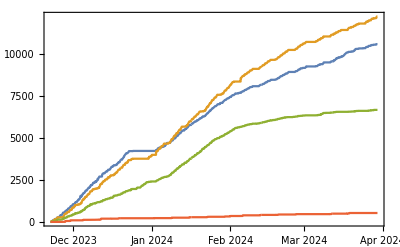

```mathematica
DateListPlot[heatStockSeason]
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockSeason.mx",heatStockSeason];
```

```mathematica
heatStockSeason=Import[NotebookDirectory[]<>"\\heatStockSeason.mx"];
```

```mathematica
heatStockDaily=Table[
Module[
{dailyCumulative},
dailyCumulative=SelectElementsByDateRange[heatStockSeason[[cycle]],DateExtend[day,0,0],DateExtend[day,23,59]];
Transpose[{
Transpose[dailyCumulative][[1]],
Transpose[dailyCumulative][[2]]-dailyCumulative[[1]][[2]]
}]
]
,{day,heatDataDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDaily.mx",heatStockDaily];
```

```mathematica
heatStockDaily=Import[NotebookDirectory[]<>"\\heatStockDaily.mx"];
```

## gáz

```mathematica
gasDataDays=Map[DateObject,Join[
DateRange[{2023,11,23},{2023,12,6}],
DateRange[{2023,12,15},{2024,5,16}]
]];
```

```mathematica
gasStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\gas_stock.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,gasDataDays]]];
```

```mathematica
gasStockDaily=Table[
Module[
{dayDateList},
dayDateList=DateList[gasDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[gasStockLine[[1]]];
Transpose[{DateObject[dayDateList],gasStockLine[[2]]}]
,{gasStockLine,gasStockPre[[dayN]]}]
]
,{dayN,1,Length[gasDataDays]}];
```

```mathematica
Export[NotebookDirectory[]<>"\\gasStockDaily.mx",gasStockDaily];
```

```mathematica
gasStockDaily=Import[NotebookDirectory[]<>"\\gasStockDaily.mx"];
```

## szobák hőmérséklete

```mathematica
roomTempDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
roomTempsPre=Table[Quiet[
Map[
Import[formattedDataRoot<>"\\"<>#<>"\\room_"<>ToString[room]<>"_temps.csv"]
&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,roomTempDataDays]]
],{room,1,10}];
```

```mathematica
roomTempsDaily=Quiet[Table[Table[
Module[
{dayDateList},
dayDateList=DateList[roomTempDataDays[[dayN]]];
If[
Dimensions[roomTempsPre[[room]][[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[roomTempLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],roomTempLine[[2;;5]]}]
,{roomTempLine,roomTempsPre[[room]][[dayN]]}]],
None
]
]
,{dayN,1,Length[roomTempDataDays]}],{room,1,10}]];
```

```mathematica
Export[NotebookDirectory[]<>"\\roomTempsDaily.mx",roomTempsDaily];
```

```mathematica
roomTempsDaily=Import[NotebookDirectory[]<>"\\roomTempsDaily.mx"];
```

```mathematica
setTempLowForAtLeastOneRoomDaily=Transpose[
{roomTempDataDays,
Quiet[Map[
Min[#]<0&,
Transpose[Table[
Table[
Min[Select[Transpose[roomTemp[[1]]][[2]]-Transpose[roomTemp[[2]]][[2]],NumberQ]]
,{roomTemp,roomTempsDaily[[room]]}]
,{room,1,10}]]
]]
}];
```

## fűtési állapot

```mathematica
heatingStateDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
heatingStatePre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heating_state.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatingStateDataDays]]];
```

```mathematica
heatingStateDaily=Table[
Module[
{dayDateList},
dayDateList=DateList[heatingStateDataDays[[dayN]]];
If[
Dimensions[heatingStatePre[[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatingStateLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],5],heatingStateLine[[2;;6]]}]
,{heatingStateLine,heatingStatePre[[dayN]]}]],
None
]
]
,{dayN,1,Length[heatingStateDataDays]}];
```

```mathematica
Position[heatingStateDaily,None]
```

{{56},{57},{96},{97},{110},{111},{119},{120},{138},{145},{146},{152},{153},{154},{157},{158},{159},{160},{161},{162},{163},{167},{168},{173},{174},{175},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192}}

```mathematica
heatingStateNoDataDays=heatingStateDataDays[[Flatten[Position[heatingStatePre,$Failed]]]];
```

```mathematica
noHeatingDays=Transpose[Select[setTempLowForAtLeastOneRoomDaily,#[[2]]==False&]][[1]];
```

```mathematica
Table[
Module[
{dayDateList,minutes,blankDayData,dayPosition},
dayDateList=DateList[day];
minutes=Map[
DateObject[Join [dayDateList[[1;;3]],MinuteOfDayToHourAndMinuteList[#]]]&
,Transpose[heatingStatePre[[1]]][[1]]];
blankDayData=ConstantArray[
Transpose[
{
minutes,
ConstantArray[0,288]
}
],5];
dayPosition=Position[heatingStateDataDays,day][[1]][[1]];
heatingStateDaily[[dayPosition]]=blankDayData;
]
,{day,Intersection[heatingStateNoDataDays,noHeatingDays]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Position[heatingStateDaily,None]
```

{{56},{96},{97},{110},{111},{138},{145},{152},{157},{167},{168},{173},{174},{179}}

```mathematica
Export[NotebookDirectory[]<>"\\heatingStateDaily.mx",heatingStateDaily];
```

```mathematica
heatingStateDaily=Import[NotebookDirectory[]<>"\\heatingStateDaily.mx"];
```

## egyéb

## elemzés

úgy érdemes tekinteni, mint egy cél felé hajtott rendszert

kontrollváltozók:
	- fő kontrollváltozók: fogyasztott gáz és kiküldött hő
		> korrellált kontrollváltozók: fűtési állapot
	- nem irányított kontrollváltozó: kinti hőmérséklet, besugárzás
függő változók: szobák hőmérséklete

hibajel: beállított hőmérséklet - aktuális hőmérséklet